# StateModelRnD

There are two methods for using StateModelRnD, one is to install the Mathematica package on your computer and to write Mathematica scripts to solve and interact with the solution. The other is to use the web interface. This notebook will focus on how to interact with StateModelRnD in a Mathematica notebook.

Before we begin we need to import StateModelRnD.

```mathematica
SetDirectory[NotebookDirectory[]];
<<State`
```

Now that StateModelRnD has been imported we can start working on a problem. In this case we will be working on the problem set forth in the tutorial. This problem consists of a motor powering a pump through a flexible shaft. This pump pushes water through an elbow with a known resistance and out into the atmosphere. A diagram of the physical system can be seen below,

The following equations for this system were found in the tutorial :

```mathematica
inVars={Vs};
stateVarElEqns={
tk'==kt wk
};
otherElEqns={
vR==R iR,
vL==L iL',
i1==-Kv t2,
w2==Kv v1,
w3==Q4/-DD,
P4==t3/DD,
QR==PR/Rf
};
constraints={
iL->i1,
iR->i1,
t2->-tk,
t3->tk,
Q4->QR,
v1->Vs-vR-vL,
wk->w2-w3,
PR->P4
};
outputVars={QR};
```

Now using the State command the solution can be found.

```mathematica
State[inVars,stateVarElEqns,otherElEqns,constraints,outputVars];
```

Now that the solution has been found, different parts of the equation can be viewed including the A matrix,

```mathematica
a
```

{{(kt (1-DD^2 Kv^2 R Rf))/(DD^2 (Rf+kt Kv^2 L Rf))}}

the state equation,

```mathematica
StEqn
```

{(kt (tk[t]-DD^2 Kv^2 R Rf tk[t]+DD^2 Kv Rf Vs[t]))/(DD^2 (Rf+kt Kv^2 L Rf))}

or the transfer function,

```mathematica
TfM
```

{{(DD kt Kv)/(DD^2 Rf s+kt (-1+DD^2 Kv^2 Rf (R+L s)))}}

The results can also be viewed in other languages such as LaTeX,

```mathematica
a//TeXForm
```

\left(
\begin{array}{c}
 \frac{\text{kt} \left(1-\text{DD}^2 \text{Kv}^2 R
   \text{Rf}\right)}{\text{DD}^2 \left(\text{kt} L \text{Rf}
   \text{Kv}^2+\text{Rf}\right)} \\
\end{array}
\right)

Other Mathematica functions can be used to manipulate the equations. At this point let’s solve the differential equation,

```mathematica
input=Vs[t]->12;
ic=tk[0]==0;
x=tk[t]/.DSolve[{tk'[t]==StEqn[[1]]/.input, ic}, tk[t],t]
```

{(12 DD^2 ⅇ^(-(kt Kv^2 R t)/(1+kt Kv^2 L)+(kt t)/(DD^2 (1+kt Kv^2 L) Rf)) (-1+ⅇ^((kt (-1+DD^2 Kv^2 R Rf) t)/(DD^2 (1+kt Kv^2 L) Rf))) Kv Rf)/(-1+DD^2 Kv^2 R Rf)}

Using this solution of the state variable we can find the output of the system.

```mathematica
y=c x+d Vs[t]/.input
```

{{(12 DD ⅇ^(-(kt Kv^2 R t)/(1+kt Kv^2 L)+(kt t)/(DD^2 (1+kt Kv^2 L) Rf)) (-1+ⅇ^((kt (-1+DD^2 Kv^2 R Rf) t)/(DD^2 (1+kt Kv^2 L) Rf))) Kv)/(-1+DD^2 Kv^2 R Rf)}}

In order to plot the response let’s substitute in values for the variables.

```mathematica
values={
R->5,
L->0.1,
Kv->1000,
kt->10,
DD->0.0015,
Rf->4 10^6
};
```

Given these values the solution of the differential equation is,

```mathematica
y/.values
```

{{4.×10^-7 ⅇ^(-49.9999 t) (-1+ⅇ^(49.9999 t))}}

Finally this output can be plotted to view the response.

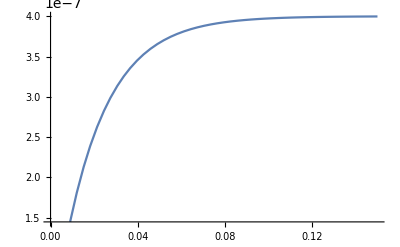

```mathematica
Plot[y/.values/.t->tt,{tt,0,0.15}]
```